# Lecture 02 by Chi-Ok Hwang

## Fun Facts

### Mathematica 1.0 was released at June 1988.

#### References

Wolfram 언어 버전 기록

### Steve Jobs suggested the name, “Mathematica.”; mathesis --> mathematikos (그리스어) --> mathematica (라틴어) --> Mathematics

-Graphics-

#### References

A Few Memories

### Wolfram’s R&D staffs involved to provide Mathematical aspects in the Numb3rs.

-Graphics-

#### References

The Math behind Numb3rs

### The language was officially named only in June 2013.

-Graphics-

#### References

Wolfram Language

## We will cover the following textbook selectively before midterm exam.

[1] S. Wolfram, An Elementary Introduction to the Wolfram Language, 2nd ed. Wolfram Media, Inc., 2017.

-Graphics-

Preview videos

### Programming paradigm

1.  Procedual languages
2.  Object-oriented programming
3. Visual programming
4. Functional programming
5. Imperative programming
6. Dataflow programming

## Preface

Preface

## What is the Wolfram Language?

What Is the Wolfram Language?

a computer language

knowledge based

Wofram|Alpha

## Practicalities of Using the Wolfram Language

Practicalities of Using the Wolfram Language

Keyboard Shortcut Listing

## Other Resources

Other Resources

## 1 Starting Out: Elementary Arithmetic

1 Starting Out: Elementary Arithmetic

The file that changes  the input cell background color is Default.nb

```mathematica
1234 5678
```

7006652

How to control precision in mathematica

```mathematica
N[Pi, 100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

## 2 Introducing Functions

2 Introducing Functions

```mathematica
Max[4,7,25]
```

25

```mathematica
RandomInteger[100]
```

78

## 3 First Look at Lists

3 First Look at Lists

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
Join[Range[3], Range[4]]
```

{1,2,3,1,2,3,4}

## 4 Displaying Lists

4 Displaying Lists

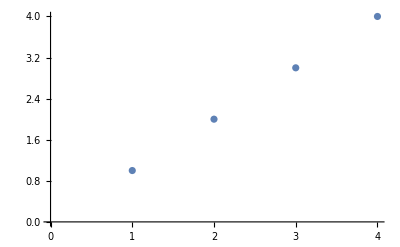

```mathematica
ListPlot[Range[4]]
```

```mathematica
PieChart[{3,4,3}]
```

-Graphics-

```mathematica
PieChart3D[{1,1,1},SectorOrigin->{Automatic,1}]
```

-Graphics3D-

## 5 Operations on Lists

5 Operations on Lists

Arithmetic with lists

Plot

Sort

Length

Total

Count

First, Last, Part

Min, Max

IntegerDigits

Take, Drop

...

Picky exercises: 2, 5, 7, 9, +4

## 6 Making Tables

6 Making Tables

```mathematica
Table[4,3]
```

{4,4,4}

```mathematica
Table[{123},3]
```

{{123},{123},{123}}

```mathematica
Table[n+2,{n,4}]
```

{3,4,5,6}

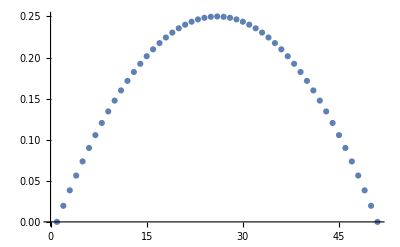

```mathematica
ListPlot[Table[x-x^2,{x,0,1,.02}]]
```

## 7 Color and Styles

7 Colors and Styles

```mathematica
Table[Style[x,RandomColor[],RandomInteger[30]],25]
```

{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}

## 8 Basic Graphics Objects

8 Basic Graphics Objects

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
{Graphics3D[Cone[]],Graphics3D[Cylinder[]]}
```

{-Graphics3D-,-Graphics3D-}